```mathematica
Needs["Cosmology`Defs`"]
Needs["Cosmology`EH98`"]
```

#### Plot P(k)

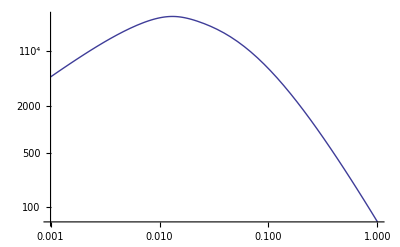

```mathematica
LogLogPlot[pkEH[k,1.0, 3. 10^-9, FoMSWG], {k, 10^-3, 1}]
```

```mathematica
pk1[k_] := pkEH[k, 1.0, 3. 10^-9, FoMSWG];
```

```mathematica
sigmaR[pk1]
```

0.819531

```mathematica
sigmaR[pk1, 50.0]
```

0.16246

```mathematica
sigmaR[pk1, 100.0]
```

0.0698389

```mathematica
getOscillatoryIntegralOpts[]
```

{Method→{SymbolicPreprocessing,OscillatorySelection→True,InterpolationPointsSubdivision→False},PrecisionGoal→4,MaxRecursion→20}

```mathematica
setOscillatoryIntegralOpts[{MaxRecursion->30, WorkingPrecision->MachinePrecision}]
```

{MaxRecursion→30,WorkingPrecision→MachinePrecision,Method→{SymbolicPreprocessing,OscillatorySelection→True,InterpolationPointsSubdivision→False},PrecisionGoal→4}

```mathematica
sigmaR[pk1, 10000.0, 0.0,10*^4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0000232276

```mathematica
(* Simplify life by just calculating points before hand *)
rarr = 10^Range[1.0, Log10[1000.0], 0.05];
```

```mathematica
sigarr = sigmaR[pk1, #, 0.0, 1000.0] & /@ rarr;
```

```mathematica
sigplot = ListLogLogPlot[Transpose[{rarr, sigarr}], PlotRange->Full, Frame->True, FrameLabel-> {"R (Mpc/h)", "σ(R)"}, LabelStyle->20];
```

```mathematica
p1 = LogLogPlot[# (r/10)^(-3/2), {r, 1.0, 1000.0}, PlotStyle->{Dashed,Red}] & /@ {0.7, 1.4, 2.8, 5.6};
```

Power::infy: Infinite expression 1/0.^3/2 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

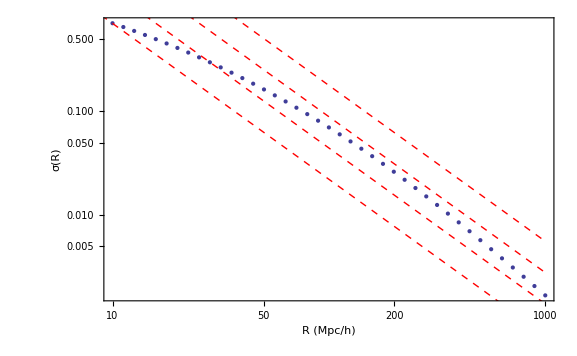

```mathematica
out = Show[{sigplot, p1}]
```

```mathematica
sigmaR[pk1, 0.001, 0.0, 500.0]/sigmaR[pk1, 0.001, 0.0, 1000.0]
```

1.

```mathematica
Export["~/Desktop/sigmaR.png", out, ImageSize-> 72*{18,12}]
```

~/Desktop/sigmaR.png

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.